```mathematica
raw = "-40.0, 9.378145351184969e-05, 1.9959774558024788e-05
-39.8, 8.97857290339221e-05, 1.8230450442008515e-05
-39.599999999999994, 8.577989852719429e-05, 1.6507107160339738e-05
-39.39999999999999, 8.179628575696151e-05, 1.4849633952118727e-05
-39.19999999999999, 7.774479102055257e-05, 1.6070416364656295e-05
-38.999999999999986, 7.379426143487664e-05, 1.7533030575700994e-05
-38.79999999999998, 6.977696231365898e-05, 1.9048276074970283e-05
-38.59999999999998, 6.586705470168753e-05, 2.0381644819718806e-05
-38.39999999999998, 6.19650430971177e-05, 2.2267206601422512e-05
-38.199999999999974, 5.804034804657607e-05, 2.429752106994157e-05
-37.99999999999997, 5.4195315310462844e-05, 2.6480709165742796e-05
-37.79999999999997, 5.0361147848732885e-05, 2.8757813377441442e-05
-37.599999999999966, 4.6563748085549576e-05, 3.124579681478036e-05
-37.39999999999996, 4.2756807868229204e-05, 3.395208315660054e-05
-37.19999999999996, 3.900701641561678e-05, 3.673054337119355e-05
-36.99999999999996, 3.525688401264442e-05, 3.9531980567864615e-05
-36.799999999999955, 3.150005992817387e-05, 4.2707299012200575e-05
-36.59999999999995, 2.778452472387647e-05, 4.617471002355952e-05
-36.39999999999995, 2.4053156207867803e-05, 4.988201928903666e-05
-36.199999999999946, 2.0369557890168813e-05, 5.4223077812973715e-05
-35.99999999999994, 1.6709612164243435e-05, 5.9036718699870133e-05
-35.79999999999994, 1.3067195991578317e-05, 6.33275527734132e-05
-35.59999999999994, 9.455333876618022e-06, 6.70119236520534e-05
-35.399999999999935, 5.827464385409059e-06, 8.131096055762715e-05
-35.19999999999993, 3.6838018111077202e-06, 4.2732949872582435e-05
-34.99999999999993, 5.715093974274473e-06, 2.78064803214939e-05
-34.799999999999926, 8.13289294984098e-06, 2.0120206561539405e-05
-34.59999999999992, 1.073033957318294e-05, 1.6549303684797975e-05
-34.39999999999992, 1.354922203110769e-05, 1.4647335452052567e-05
-34.19999999999992, 1.643394382137067e-05, 1.406395136223573e-05
-33.999999999999915, 1.9261964049984415e-05, 1.4845970800594885e-05
-33.79999999999991, 2.2187378809897868e-05, 1.6223897635414434e-05
-33.59999999999991, 2.5196625887767392e-05, 1.8266539887085607e-05
-33.399999999999906, 2.8181574598289122e-05, 2.0556718892827972e-05
-33.1999999999999, 3.1112600025592624e-05, 2.3017289133885643e-05
-32.9999999999999, 3.402009671325123e-05, 2.5948093487648086e-05
-32.7999999999999, 3.68825417163003e-05, 2.9178945659530277e-05
-32.599999999999895, 3.9718738076575634e-05, 3.247312332061412e-05
-32.39999999999989, 4.2629740466471987e-05, 3.571458470675246e-05
-32.19999999999989, 4.547447822377075e-05, 3.8924352452799465e-05
-31.999999999999886, 4.8384050254734086e-05, 4.215987704176041e-05
-31.799999999999883, 5.127864810405317e-05, 4.5431682739765784e-05
-31.59999999999988, 5.4194532927032755e-05, 4.8625143764874106e-05
-31.399999999999878, 5.713662822209263e-05, 5.175062189725079e-05
-31.199999999999875, 6.006325716899366e-05, 5.491623444894867e-05
-30.999999999999872, 6.305289549077407e-05, 5.797155832032913e-05
-30.79999999999987, 6.603518363835016e-05, 6.081433889365378e-05
-30.599999999999866, 6.899482488964776e-05, 6.372067475224565e-05
-30.399999999999864, 7.192933739698518e-05, 6.661860012887191e-05
-30.19999999999986, 7.49055652812076e-05, 6.957917187283734e-05";

data = ImportString[raw]
```

{{-40.,0.0000937815,0.0000199598},{-39.8,0.0000897857,0.0000182305},{-39.6,0.0000857799,0.0000165071},{-39.4,0.0000817963,0.0000148496},{-39.2,0.0000777448,0.0000160704},{-39.,0.0000737943,0.000017533},{-38.8,0.000069777,0.0000190483},{-38.6,0.0000658671,0.0000203816},{-38.4,0.000061965,0.0000222672},{-38.2,0.0000580403,0.0000242975},{-38.,0.0000541953,0.0000264807},{-37.8,0.0000503611,0.0000287578},{-37.6,0.0000465637,0.0000312458},{-37.4,0.0000427568,0.0000339521},{-37.2,0.000039007,0.0000367305},{-37.,0.0000352569,0.000039532},{-36.8,0.0000315001,0.0000427073},{-36.6,0.0000277845,0.0000461747},{-36.4,0.0000240532,0.000049882},{-36.2,0.0000203696,0.0000542231},{-36.,0.0000167096,0.0000590367},{-35.8,0.0000130672,0.0000633276},{-35.6,9.45533×10^-6,0.0000670119},{-35.4,5.82746×10^-6,0.000081311},{-35.2,3.6838×10^-6,0.0000427329},{-35.,5.71509×10^-6,0.0000278065},{-34.8,8.13289×10^-6,0.0000201202},{-34.6,0.0000107303,0.0000165493},{-34.4,0.0000135492,0.0000146473},{-34.2,0.0000164339,0.000014064},{-34.,0.000019262,0.000014846},{-33.8,0.0000221874,0.0000162239},{-33.6,0.0000251966,0.0000182665},{-33.4,0.0000281816,0.0000205567},{-33.2,0.0000311126,0.0000230173},{-33.,0.0000340201,0.0000259481},{-32.8,0.0000368825,0.0000291789},{-32.6,0.0000397187,0.0000324731},{-32.4,0.0000426297,0.0000357146},{-32.2,0.0000454745,0.0000389244},{-32.,0.0000483841,0.0000421599},{-31.8,0.0000512786,0.0000454317},{-31.6,0.0000541945,0.0000486251},{-31.4,0.0000571366,0.0000517506},{-31.2,0.0000600633,0.0000549162},{-31.,0.0000630529,0.0000579716},{-30.8,0.0000660352,0.0000608143},{-30.6,0.0000689948,0.0000637207},{-30.4,0.0000719293,0.0000666186},{-30.2,0.0000749056,0.0000695792}}

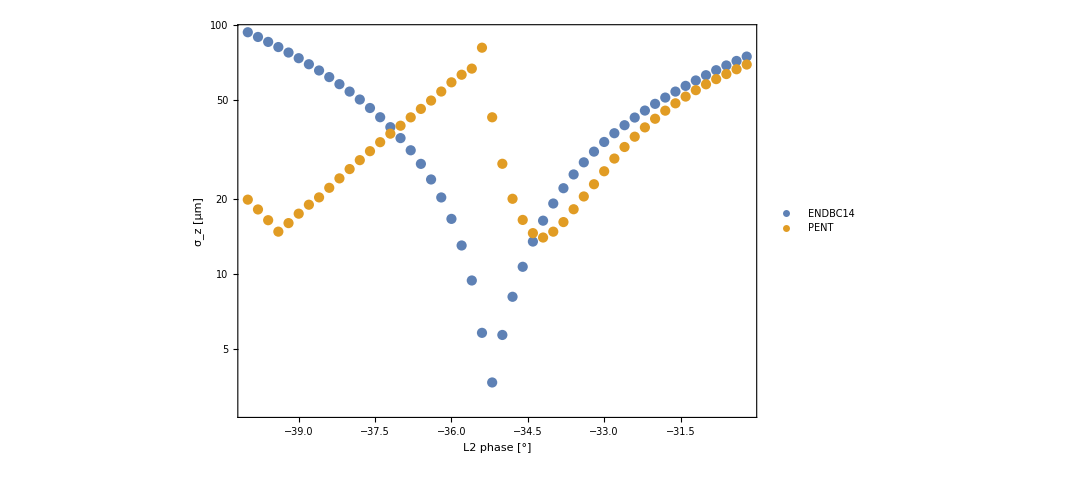

```mathematica
ListLogPlot[
{
{#[[1]],10^6*#[[2]]}&/@data[[All,{1,2}]],
{#[[1]],10^6*#[[2]]}&/@data[[All,{1,3}]]
},
Frame->True,
FrameLabel->{"L2 phase [°]", "σ_z [μm]"},
PlotLegends->Placed[{"ENDBC14", "PENT"},{0.9,0.1}],
ImageSize->800,
LabelStyle->20
]
```

-Graphics-

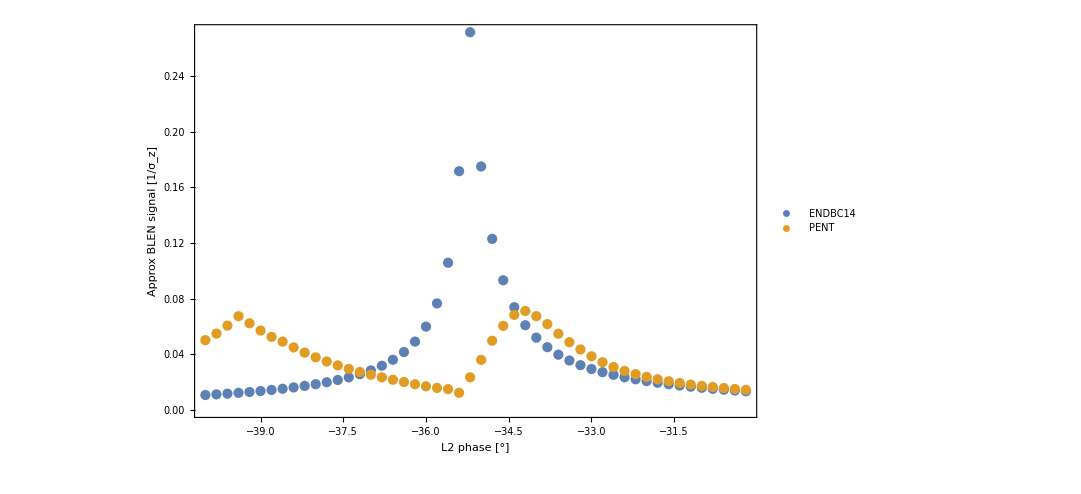

```mathematica
ListPlot[
{
{#[[1]],1/(10^6*#[[2]])}&/@data[[All,{1,2}]],
{#[[1]],1/(10^6*#[[2]])}&/@data[[All,{1,3}]]
},
Frame->True,
FrameLabel->{"L2 phase [°]", "Approx BLEN signal [1/σ_z]"},
PlotLegends->Placed[{"ENDBC14", "PENT"},{0.9,0.1}],
ImageSize->800,
LabelStyle->20,
PlotRange->All
]
```

FittedModel[…]

1+Abs[10.2221+43.7469 Abs[34.8556+x]^1.56469]^0.706089

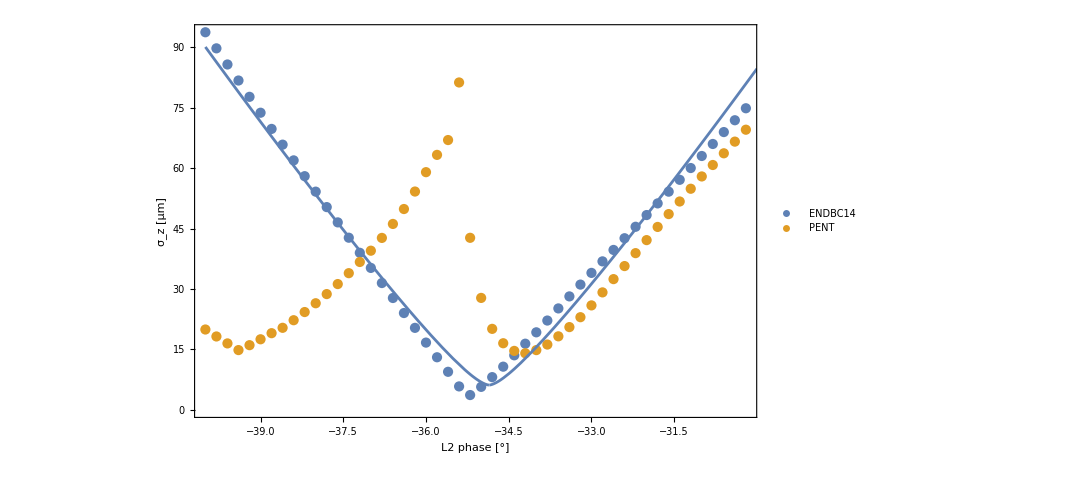

```mathematica
activeData ={#[[1]],10^6*#[[2]]}&/@data[[All,{1,2}]];
expr = 1+Abs[(b+Abs[c*(x-x0)]^m)]^n;
nlm=NonlinearModelFit[
activeData,
expr,
{b,c,x0,m,n},
x,
MaxIterations->5000,
Method->{"NMinimize",Method->"DifferentialEvolution"}
]

nlm["BestFit"]

Show[
ListPlot[
{
{#[[1]],10^6*#[[2]]}&/@data[[All,{1,2}]],
{#[[1]],10^6*#[[2]]}&/@data[[All,{1,3}]]
},
Frame->True,
FrameLabel->{"L2 phase [°]", "σ_z [μm]"},
PlotLegends->Placed[{"ENDBC14", "PENT"},{0.9,0.1}],
ImageSize->800,
LabelStyle->20
],
Plot[ nlm["BestFit"],{x,-40,-30},PlotRange->{1,100}]
]
```